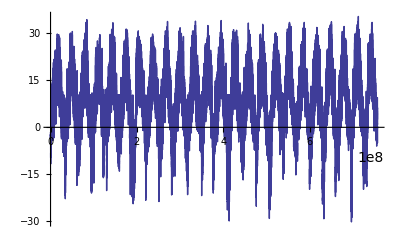

```mathematica
starttime={1990};
endtime = {2013};
city = "Sokal";
station = WeatherData["Sokal"];
coordinates = Rationalize[CityData[city,"Coordinates"]];
axialtilt=Rationalize[22.33];
entity = "Temperature";
temp = WeatherData[station,entity,{starttime,endtime}];
abstime = AbsoluteTime/@temp[[All,1]]-AbsoluteTime[starttime];
templist = Rationalize[temp[[All,2]]/.Missing["NotAvailable"]->8.2+RandomReal[{-3,3}]];
tempabs = {abstime,templist};
ListPlot[Transpose[tempabs],Joined->True]
Export["D:\\Documents\\Documents and Files\\Projects\\Aeroponycs and Orangery"<>"\\" <> station <> "_"<>entity<>"_from_"<>"1990"<>"_to_"<>"2013"<>".mat",tempabs];
```

```mathematica
Rx:=RotationMatrix[#,{1,0,0}]&;
Ry:=RotationMatrix[#,{0,1,0}]&;
Rz:=RotationMatrix[#,{0,0,1}]&;
R:=Rx[Pi/2-#2[[1]]].Rz[2 #1 Pi].Rx[#2[[2]]].Rz[(2 #1 Pi)/365-Pi/2]&;
Rmax:=Rx[Pi/2-#2[[1]]].Rz[(366 2 #1)/365-Pi].Rx[#2[[2]]].Rz[Pi/2]&;
```

```mathematica
Manipulate[Graphics3D[Tube[{Rx[Pi/2-coordinates[[1]]].Rz[2θ Pi ].Rx[Pi/2-axialtilt].Rz[(2θ Pi)/365].{1,0,0},{0,0,0}}],PlotRange->{{-1,1},{-1,1},{-1,1}}],{θ,0,365}]
```

```mathematica
WeatherData["CWO33177","Coordinates"]
```

WeatherData::notent: "\"CWO33177\"" is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

WeatherData[CWO33177,Coordinates]

```mathematica
WeatherData["Sokal"]
```

WMO33177

```mathematica
CityData["Sokal","Coordinates"]
```

{50.48,24.28}